```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;rep={a1->Subscript[a, 1],a2->Subscript[a, 2],κi->Subscript[κ, i],κr->Subscript[κ, r], ky->Subscript[k, y], kz->Subscript[k, z], vz->Subscript[v, z], vp->Subscript[v, p],en->e,b1->Subscript[b, 1],b2->Subscript[a, 2]};
ass=Assumptions->{ky,kz,κi,κr,θ,ϕ,en}∈ Reals &&  k>0  && v>0 && vz>0;
ass={k,θ,ϕ,kx,ky,kz}∈ Reals &&  k>0;
sx=({{0, 1/(√2), 0}, {1/(√2), 0, 1/(√2)}, {0, 1/(√2), 0}});sy=1/(√2)({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}});sz=({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});id=IdentityMatrix[3];

Clear[ham,ψ,eval,en,evec,α,M];
{dx,dy,dz}={kx, ky,kz};
dx Sx+dy Sy+dz Sz/.dx->-ⅈ Dx
ham=fx sx+fy sy+fz sz;
```

-ⅈ Dx Sx+ky Sy+kz Sz

```mathematica
{sx.sy-sy.sx==ⅈ sz,sx.sz-sz.sx==-ⅈ sy,sy.sz-sz.sy==ⅈ sx}//FullSimplify
```

{True,True,True}

```mathematica
(* square of the 3 matrices *)
{sx.sx//MatrixForm,sy.sy//MatrixForm,sy.sy//MatrixForm};
Eigenvalues[ham]//FullSimplify
```

{0,-√(fx^2+fy^2+fz^2),√(fx^2+fy^2+fz^2)}

```mathematica
(* they do not anticummute *)
{sx.sy+sy.sx//MatrixForm,sx.sz+sz.sx//MatrixForm,sy.sz+sz.sy//MatrixForm}//FullSimplify
```

{(0 | 0 | -ⅈ
0 | 0 | 0
ⅈ | 0 | 0),(0 | 1/(√2) | 0
1/(√2) | 0 | -1/(√2)
0 | -1/(√2) | 0),(0 | -ⅈ/(√2) | 0
ⅈ/(√2) | 0 | ⅈ/(√2)
0 | -ⅈ/(√2) | 0)}

```mathematica
Clear[ψ,eq0,eq,eqn,sol,κ,κr,κi,a1,a2,b1,b2];
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1,a2+ⅈ b2};
ψdag={1,a1-ⅈ b1,a2-ⅈ b2};
prod=2FullSimplify[ψdag.(sx.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
eq=2FullSimplify[ⅈ κ  sx.ψ+ky sy.ψ+kz sz.ψ -en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
Clear[κ,κi,en];
solu=FullSimplify[Solve[ eq0[[1]]==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0  && κr≠0,{en,κr,κi,a1,b1,a2,b2}],ass]
sol[ky_,kz_]={en,κr}/.solu;
Clear[κ,κi,b1,b2,en];
```

{2 √2 (a1+a1 a2+b1 b2),0}

{-2 en+2 kz-√2 (a1 κi+b1 (-ky+κr)),-√2 (b1 κi+a1 (ky-κr)),-2 a1 en-√2 (-b2 ky+κi+a2 κi+b2 κr),-2 b1 en+√2 (ky-a2 ky-b2 κi+κr+a2 κr),-2 a2 (en+kz)-√2 (a1 κi+b1 (ky+κr)),-2 b2 (en+kz)+√2 (-b1 κi+a1 (ky+κr))}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{en→0,κr→ky+(√2 b1 kz)/(a1^2+b1^2),κi→(√2 a1 kz)/(a1^2+b1^2),a2→-(√2 b1 ky+kz)/kz,b2→(√2 a1 ky)/kz},{en→0,κr→ky+(√2 kz)/b1,κi→0,a1→0,a2→-(√2 b1 ky+kz)/kz,b2→0},{en→-kz+(2 √2 b1 ky+4 kz)/(2+b1^2),κr→((-2+b1^2) ky+2 √2 b1 kz)/(2+b1^2),κi→0,a1→0,a2→-b1^2/2,b2→0},{en→0,κr→ky,κi→(√2 kz)/a1,b1→0,a2→-1,b2→(√2 a1 ky)/kz},{en→kz,κr→-ky,κi→0,a1→0,b1→0,a2→0,b2→0},{en→0,κr→ky+ⅈ kz,κi→0,a1→0,b1→-ⅈ √2,a2→-1+(2 ⅈ ky)/kz,b2→0},{en→0,κr→ky-ⅈ kz,κi→0,a1→0,b1→ⅈ √2,a2→-1-(2 ⅈ ky)/kz,b2→0}}

```mathematica
(* smallest value of b1^2 is 0 => this is what gives the 5th soln, viz. {en->kz,κr->-ky,κi->0,a1->0,b1->0,a2->0,b2->0} *)
```

```mathematica
g={-ⅈ ky-√2 (a1+ⅈ b1) (en-kz)-κi+ⅈ κr,-√2 en+(ⅈ a1-ⅈ a2-b1+b2) ky-(a1+a2+ⅈ (b1+b2)) (κi-ⅈ κr),-√2 (a2+ⅈ b2) (en+kz)+ⅈ (ky+ⅈ κi+κr)}/.rep
TeXForm[ +ⅈ (Subscript[k, y]+ⅈ Subscript[κ, i]+Subscript[κ, r])//FullSimplify]
```

{-ⅈ k_y-√2 (a_1+ⅈ b_1) (e-k_z)-κ_i+ⅈ κ_r,-√2 e+(ⅈ a_1+(1-ⅈ) a_2-b_1) k_y-(a_1+a_2+ⅈ (a_2+b_1)) (κ_i-ⅈ κ_r),(-1-ⅈ) √2 a_2 (e+k_z)+ⅈ (k_y+ⅈ κ_i+κ_r)}

i \left(i \kappa _i+k_y+\kappa _r\right)

```mathematica
Clear[ψ,eq0,eq,eqn,sol,κ,κr,κi,a1,a2,b1,b2];
κ=κr+ⅈ κi;
ψ={a1+ⅈ b1,1,a2+ⅈ b2};
ψdag={a1-ⅈ b1,1,a2-ⅈ b2};
prod=FullSimplify[ψdag.(sx.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
eq=√2 FullSimplify[ⅈ κ  sx.ψ+ky sy.ψ+kz sz.ψ -en id.ψ,ass]//FullSimplify
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
Clear[κ,κi,en];
solu=FullSimplify[Solve[ eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0  && κr≠0,{en,κr,κi,a1,b1,a2,b2}],ass]
Clear[κ,κi,κr,a2,b1,b2,en];
```

{√2 (a1+a2),0}

{-ⅈ ky-√2 (a1+ⅈ b1) (en-kz)-κi+ⅈ κr,-√2 en+(ⅈ a1-ⅈ a2-b1+b2) ky-(a1+a2+ⅈ (b1+b2)) (κi-ⅈ κr),-√2 (a2+ⅈ b2) (en+kz)+ⅈ (ky+ⅈ κi+κr)}

{√2 a1 (-en+kz)-κi,-ky+√2 b1 (-en+kz)+κr,-√2 en-(a1+a2) κi+b2 (ky-κr)-b1 (ky+κr),-((b1+b2) κi)+a2 (-ky+κr)+a1 (ky+κr),-√2 a2 (en+kz)-κi,ky-√2 b2 (en+kz)+κr}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{en→0,κr→ky-√2 b1 kz,κi→√2 a1 kz,a2→-a1,b2→-b1+(√2 ky)/kz},{en→kz-(2 (√2 b1 ky+kz))/(1+2 b1^2),κr→(ky-2 b1^2 ky-2 √2 b1 kz)/(1+2 b1^2),κi→0,a1→0,a2→0,b2→-1/(2 b1)},{en→0,κr→ky-√2 b1 kz,κi→0,a1→0,a2→0,b2→-b1+(√2 ky)/kz},{en→0,κr→ky,κi→0,a1→0,b1→0,a2→0,b2→(√2 ky)/kz},{en→0,κr→ky+ⅈ kz,κi→0,a1→0,b1→-ⅈ/(√2),a2→0,b2→(2 ky+ⅈ kz)/(√2 kz)},{en→0,κr→ky-ⅈ kz,κi→0,a1→0,b1→ⅈ/(√2),a2→0,b2→(2 ky-ⅈ kz)/(√2 kz)}}

```mathematica
Clear[ψ,eq0,eq,eqn,sol,κ,κr,κi,a1,a2,b1,b2];
κ=κr+ⅈ κi;
ψ={a1+ⅈ b1,a2+ⅈ b2,1};
ψdag={a1-ⅈ b1,a2-ⅈ b2,1};
prod=2FullSimplify[ψdag.(sx.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
eq=2FullSimplify[ⅈ κ  sx.ψ+ky sy.ψ+kz sz.ψ -en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
Clear[κ,κi,en];
solu=FullSimplify[Solve[ eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0  && κr≠0,{en,κr,κi,a1,b1,a2,b2}],ass]
Clear[κ,κi,κr,a2,b1,b2,en];
```

{2 √2 (a2+a1 a2+b1 b2),0}

{2 a1 (-en+kz)-√2 (a2 κi+b2 (-ky+κr)),2 b1 (-en+kz)-√2 (b2 κi+a2 (ky-κr)),-2 a2 en-√2 ((1+a1) κi+b1 (ky+κr)),-2 b2 en+√2 ((-1+a1) ky-b1 κi+κr+a1 κr),-2 en-2 kz-√2 (a2 κi+b2 (ky+κr)),√2 (-b2 κi+a2 (ky+κr))}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{en→0,κr→-ky-(√2 b2 kz)/(a2^2+b2^2),κi→-(√2 a2 kz)/(a2^2+b2^2),a1→-(√2 b2 ky+kz)/kz,b1→(√2 a2 ky)/kz},{en→0,κr→-(b2 ky+√2 kz)/b2,κi→0,a1→-(√2 b2 ky+kz)/kz,b1→0,a2→0},{en→kz-(2 (√2 b2 ky+2 kz))/(2+b2^2),κr→-((-2+b2^2) ky+2 √2 b2 kz)/(2+b2^2),κi→0,a1→-b2^2/2,b1→0,a2→0},{en→0,κr→-ky,κi→-(√2 kz)/a2,a1→-1,b1→(√2 a2 ky)/kz,b2→0},{en→-kz,κr→ky,κi→0,a1→0,b1→0,a2→0,b2→0},{en→0,κr→-ky-ⅈ kz,κi→0,a1→-1+(2 ⅈ ky)/kz,b1→0,a2→0,b2→-ⅈ √2},{en→0,κr→-ky+ⅈ kz,κi→0,a1→-1-(2 ⅈ ky)/kz,b1→0,a2→0,b2→ⅈ √2}}

```mathematica
(* where κr vanishes, what is the energy value? *)
(* {en->-kz+(2 √2 b1 ky+4 kz)/(2+b1^2),κr->((-2+b1^2) ky+2 √2 b1 kz)/(2+b1^2),κi->0,a1->0,a2->-b1^2/2,b2->0} *)
Clear[aval];
aval=FullSimplify[Solve[0==((-2+b1^2) ky+2 √2 b1 kz)/(2+b1^2) ,b1],ass]
FullSimplify[-kz+(2 √2 b1 ky+4 kz)/(2+b1^2)/.aval,ass]
FullSimplify[-kz+(2 √2 b1 ky+4 kz)/(2+b1^2)/.b1->0,ass]
Clear[i,kx,ky,kz];(* correct soln for μ>0 *)
```

{{b1→-(√2 (kz+√(ky^2+kz^2)))/ky},{b1→(√2 (-kz+√(ky^2+kz^2)))/ky}}

{-√(ky^2+kz^2),√(ky^2+kz^2)}

kz

```mathematica
(* where does κr go to zero and mixes with the bulk states? 
 {en-> -kz+(2 √2 b1 ky+4 kz)/(2+b1^2),κr->((-2+b1^2) ky+2 √2 b1 kz)/(2+b1^2),κi->0,a1->0,a2->-b1^2/2,b2->0}  *)
Clear[bulkentry];bulkentry=DeleteDuplicates[FullSimplify[Solve[ -kz+(2 √2 b1 ky+4 kz)/(2+b1^2)==μ && (ky^2) +kz^2 ==μ^2,{ky,kz}],ass]]
FullSimplify[(* κr = *)((-2+b1^2) ky+2 √2 b1 kz)/(2+b1^2)/.bulkentry,ass]//Chop
Clear[bulkentry];bulkentry=DeleteDuplicates[FullSimplify[Solve[ kz==μ && (ky^2) +kz^2 ==μ^2,{ky,kz}],ass]]
FullSimplify[(* κr = *)-ky/.bulkentry,ass]//Chop
Print["***************"];
grad=FullSimplify[Grad[ -kz+(2 √2 b1 ky+4 kz)/(2+b1^2),{ky,kz}]/.bulkentry,ass];
tang1={grad[[1,2]],-grad[[1,1]]}
grad=FullSimplify[Grad[ kz,{ky,kz}]/.bulkentry,ass];
tang2={grad[[1,2]],-grad[[1,1]]}
```

{{ky→(2 √2 b1 μ)/(2+b1^2),kz→-((-2+b1^2) μ)/(2+b1^2)}}

{0}

{{ky→0,kz→μ}}

{0}

***************

{-1+4/(2+b1^2),-(2 √2 b1)/(2+b1^2)}

{1,0}

{1/3,(2 √2)/3}

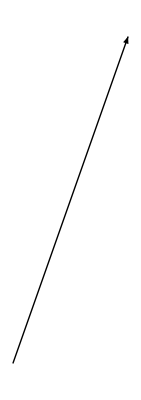

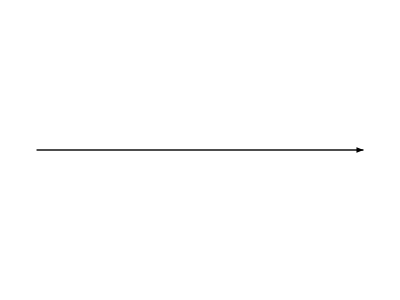

```mathematica
{-1+4/(2+b1^2),-(2 √2 b1)/(2+b1^2)}/.b1->-1
Graphics[Arrow[{{0,0},%}]]
Graphics[Arrow[{{0,0},{1,0}}]]
```

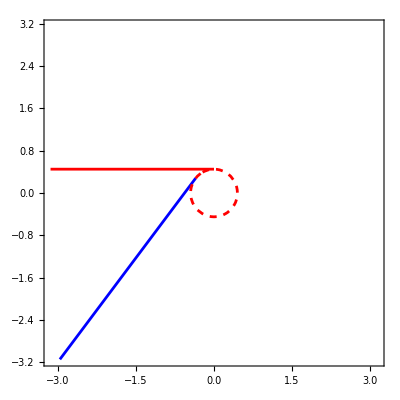

```mathematica
lim=π;mu=0.45;b1=-0.7;
(*{en->-kz+(2 √2 b1 ky+4 kz)/(2+b1^2),κr->((-2+b1^2) ky+2 √2 b1 kz)/(2+b1^2),κi->0,a1->0,a2->-b1^2/2,b2->0}*)
c1=Quiet[ContourPlot[-kz+(2 √2 b1 ky+4 kz)/(2+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Blue,RegionFunction->Function[{ky,kz,z},Chop[(-2+b1^2) ky+2 √2 b1 kz]>0 ],PlotLegends->Automatic]];
c2=Quiet[ContourPlot[kz==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Red,RegionFunction->Function[{ky,kz,z},Chop[-ky]>0 ],PlotLegends->Automatic]];
fs=ContourPlot[√(ky^2+kz^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Red,Dashed]];
Show[c1,c2,fs]
Clear[b1,i];
```

## Plot

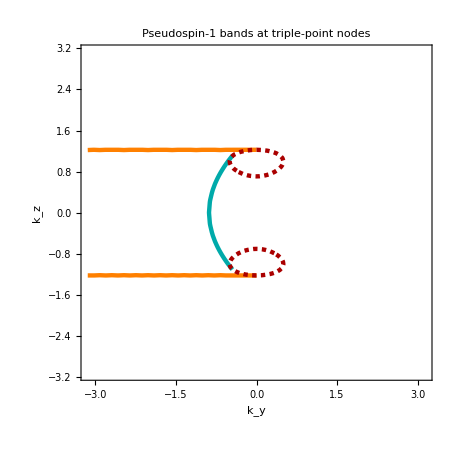

```mathematica
Clear[kzt,kyt,c1,c2,plt];lim=π;kw=1;th=0.007;kzt=kz;kyt=ky(*(ky^2-kw^2)*);
mu=0.5;b1=-1;
style={Directive[Darker[Cyan],Thickness[th]],(**)Directive[Orange,Thickness[th]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.002]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};
i=1;
(*{en->-kz+(2 √2 b1 ky+4 kz)/(2+b1^2),κr->((-2+b1^2) ky+2 √2 b1 kz)/(2+b1^2),κi->0,a1->0,a2->-b1^2/2,b2->0}*)
c1=Quiet[ContourPlot[-(kz^2-kw^2)+(2 √2 b1 ky+4 (kz^2-kw^2))/(2+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[(-2+b1^2) ky+2 √2 b1 (kz^2-kw^2)]>0 ],PlotLegends->Automatic]];
i=2;
c2=Quiet[ContourPlot[(kz^2-kw^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky]>0 ],PlotLegends->Automatic]];
fs=ContourPlot[√(ky^2+(kz^2-kw^2)^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]]];
plt=Show[c1,c2,fs,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"Pseudospin-1 bands at triple-point nodes",20,FontFamily->"TexMaths Roman",Brown,Bold]]
Clear[b1,i,kw,kzt,kyt];
SetDirectory[NotebookDirectory[]];
Export["spin1arc.pdf",Rasterize[plt],ImageResolution->100];
```

## numerical solns

```mathematica
Clear[daty];
daty[μ_,pts_]:=Module[{κr,t,κi=0,ky,kz,eq0,kx,eqn,en=μ,a1,a2,b1,b2,del=2π/pts,i,j,dat={},sol,len},
eq0=b1^2+b2^2-1;(* b1=Sin[t];b2=Cos[t];*)
eqn={-2 en+√2 a1 kx+√2 a2 ky-2 κi,√2 a2 kx-√2 a1 ky+2 κr,-2 a1 en+√2 (kx+b1 kx+b2 ky),-2 a2 en+√2 (b2 kx+ky-b1 ky),√2 a1 kx-√2 a2 ky+2 b1 (-en+κi)+2 b2 κr,√2 a2 kx+√2 a1 ky+2 b2 (-en+κi)-2 b1 κr};
For[(**)i=0,i<=pts,i++,
ky=0+i del;
sol=Chop[Quiet[NSolveValues[ eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0 && Re[κr]>0 &&  Abs[Im[κr]]<10^-6,{kx,κr,a1,a2,b1,b2},Reals]],10^-6];
len=Length[sol];
(* accumulation kx values *)
For[j=1,j<=len,j++,dat=AppendTo[dat,{sol[[j,1]],ky}](*; Print["***********"]*)]
(**)];
Sort[dat]]
daty[mu,10]
```

{{-5.05,0},{-4.95947,π/5},{-0.62975,0},{-0.503814,0},{-0.129152,π/5}}

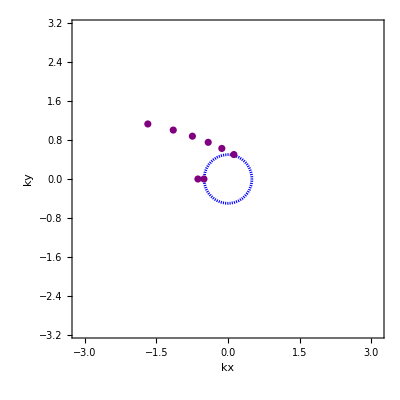

```mathematica
lim=π;mu=0.5;
(*xdat=datx[mu,40];*)
ydat=daty[mu,50];
ar1=ListPlot[{ydat},PlotRange->{-lim,lim},Frame->True,PlotStyle->Purple];
(*ymdat=daty[-mu,40];
ar2(* bottom arc *)=ListPlot[{ymdat},PlotRange->{-π,π},Frame->True,PlotStyle->Green];*)
fs=ContourPlot[√(ky^2+kx^2)==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{kx,ky},Contours->20,ContourStyle->{Directive[Red,Dashing[0.002]],Directive[Blue,Dashing[0.002]]}];
(*Show[fs,ar1,ar2]*)
Show[fs,ar1]
```